## Analysis of output from PACT

Copyright 2009-2013 Trevor Bedford

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Dropbox/current-projects/pact/source/example

## Setup

```mathematica
colorlist={RGBColor[0.857,0.131,0.132],RGBColor[0.324,0.609,0.708],RGBColor[0.765,0.728,0.274],RGBColor[0.513,0.73,0.442],RGBColor[0.394,0.113,0.593],RGBColor[0.6,0.4,0.2],RGBColor[0.251,0.225,0.769],RGBColor[0.902,0.541,0.209]};
```

```mathematica
colorrules=MapIndexed[#2[[1]]->#1&,colorlist];
```

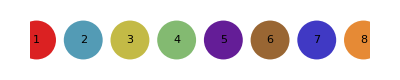

```mathematica
Graphics[MapIndexed[{PointSize[0.07],#1,Point[{First@#2,0}],Black,Text[First@#2,{First@#2,0}]}&,colorlist],ImageSize->400,AspectRatio->0.2]
```

```mathematica
n=7;
```

```mathematica
names={"China","Europe","Japan","Oceania","SouthAmerica","SoutheastAsia","USA"};
```

## Tree

```mathematica
{tips,trunk,rules,labels,coords,ids,traits}=Import["out.rules","Table"];
```

```mathematica
rules=ToExpression[rules];labels=ToExpression[labels];coords=ToExpression[coords];ids=ToExpression[ids];traits=ToExpression[traits];
```

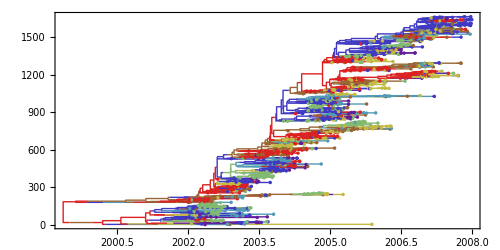

```mathematica
Graphics[{Map[{#[[1]]/.labels/.colorrules,With[{coordsA=#[[1]]/.coords,coordsB=#[[2]]/.coords},Line[{coordsA,{coordsB[[1]],coordsA[[2]]},coordsB}]]}&,rules],{PointSize[0.005],Map[{#/.labels/.colorrules,Point[(#/.coords)]}&,tips]}},ImageSize->500,AspectRatio->0.5,Frame->{True,False,False,False},FrameStyle->Directive[FontSize->9,FontFamily->"GillSans"]]
```

## Summary statistics

```mathematica
stats=Import["out.stats","Table"];
```

### Coalescence

Timescale of coalescence (N_e τ).  Equal to effective population size if time is measured in generations.

```mathematica
coalrates=Table[Flatten[Select[stats,#[[1]]=="coal_"<>ToString[i]&]],{i,n}];
```

```mathematica
coalrates=If[Length[coalrates[[1]]]>0,Round[1/coalrates[[All,{4,3,2}]],0.001],{}];
```

```mathematica
If[Length[coalrates]>0,TableForm[coalrates,TableHeadings->{names}]]
```

China | 1.532 | 1.532 | 1.532
Europe | 2.006 | 2.006 | 2.006
Japan | 1.645 | 1.645 | 1.645
Oceania | 0.565 | 0.565 | 0.565
SouthAmerica | 2.368 | 2.368 | 2.368
SoutheastAsia | 1.817 | 1.817 | 1.817
USA | 2.293 | 2.293 | 2.293

### Migration

```mathematica
migrates=Flatten[Table[Select[stats,#[[1]]=="mig_"<>ToString[i]<>"_"<>ToString[j]&],{i,n},{j,n}],2];
```

```mathematica
migrates=If[Length[migrates[[1]]]>0,Round[migrates[[All,{2,3,4}]],0.001],{}];
```

```mathematica
If[Length[migrates]>0,TableForm[migrates,TableHeadings->{names}]];
```

```mathematica
mig=Table[With[{list=Select[stats,#[[1]]=="mig_"<>ToString[i]<>"_"<>ToString[j]&]},If[Length[list]>0,list[[1,3]],0]],{i,n},{j,n}];
```

```mathematica
totalin=Total[mig];
```

```mathematica
totalout=Total[mig,{2}];
```

```mathematica
TableForm[Round[Append[Transpose[Append[Transpose[mig],totalout]],Append[totalin,0]],0.01]/. x_:>""/;x<0.01,TableHeadings->{Append[names,"Total"],Append[names,"Total"]}]
```

| China | Europe | Japan | Oceania | SouthAmerica | SoutheastAsia | USA | Total
China |  |  | 0.98 |  | 0.04 | 0.31 | 0.26 | 1.59
Europe | 0.01 |  | 0.04 | 0.18 | 0.11 | 0.27 | 0.14 | 0.76
Japan | 0.03 | 0.02 |  | 0.18 | 0.26 | 0.03 | 0.1 | 0.62
Oceania | 0.01 | 0.09 | 0.16 |  | 0.04 | 0.14 |  | 0.44
SouthAmerica | 0.03 |  | 0.06 |  |  |  | 0.04 | 0.14
SoutheastAsia | 0.4 | 0.22 | 0.47 | 0.36 | 0.07 |  | 0.12 | 1.63
USA | 0.1 | 0.65 | 0.37 | 1.27 | 0.89 | 0.19 |  | 3.47
Total | 0.59 | 0.97 | 2.07 | 2. | 1.41 | 0.94 | 0.66 |

## Skyline statistics

```mathematica
skls=Import["out.skylines","Table"];
```

### Proportions

```mathematica
start=2002;stop=2008;
```

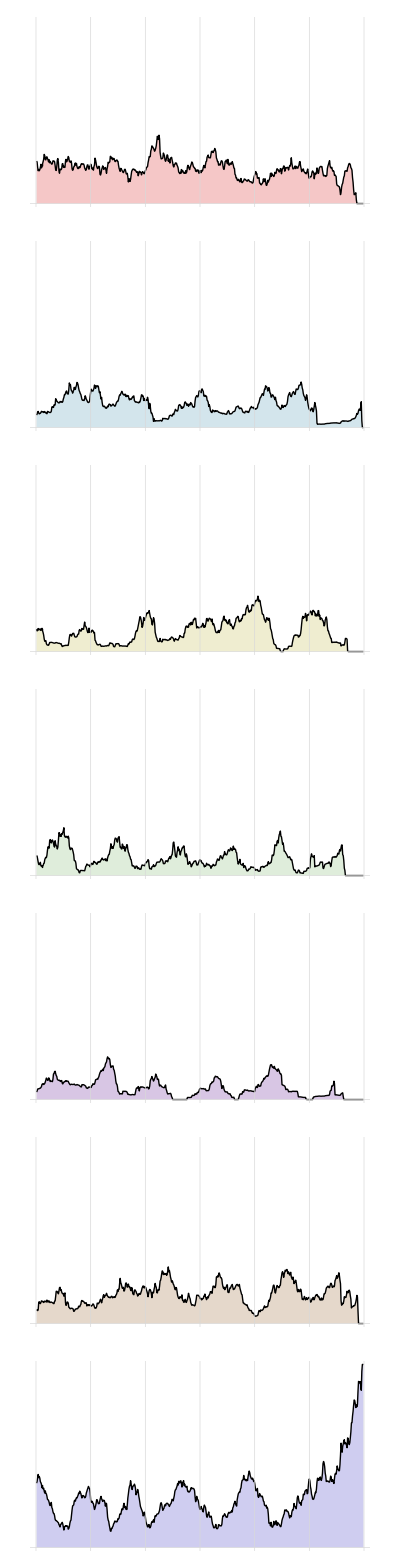

```mathematica
Grid[Table[With[{list = Select[skls,#[[1]]=="pro_"<>ToString[i]&]}, {ListLinePlot[Transpose[{list[[All, 2]], list[[All, 4]]}],PlotRange ->{0,1},Filling ->Bottom,Frame->False,Axes->False,AspectRatio->0.06,ImageSize->500,GridLines->{Range[start,stop],{0}},PlotStyle->Black,FillingStyle->Directive[Opacity[0.25],colorlist[[i]]]]}],{i, n}]]
```

## Tip statistics

```mathematica
tips=Import["out.tips","Table"];
```

### Time to trunk

```mathematica
times=Select[tips,#[[1]]=="time_to_trunk"&];
```

```mathematica
start=2002;stop=2007;
```

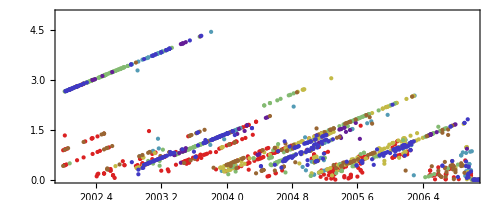

```mathematica
Graphics[Table[With[{list = Select[times, #[[3]] == i &]}, {colorlist[[i]],MapThread[Point[{#1,#2}]&,{list[[All, 4]], list[[All, 6]]}]}], {i, n}],PlotRange ->{{start,stop},{0, 5}},Frame->{True,True,False,False},AspectRatio->0.4,ImageSize->500]
```